```mathematica
test1=StringSplit[Import["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\test1.txt"],"\n"];
test2=StringSplit[Import["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\test2.txt"],"\n"];
```

```mathematica
expected1={1,2,3,4,1,2,1,5,5,4,5,2,2,4,4,4,4,3,2,5,5,4,3,3,3,3,3}/.{1->"essential",2->"extracurricular",3->"leisure",4->"school",5->"sport"};
```

```mathematica
{test1,expected1}//Transpose//TableForm
```

eat apple | essential
play piano | extracurricular
play video games | leisure
finish math homework | school
drink wine | essential
play violin | extracurricular
drink coffee | essential
play badminton | sport
play tennis | sport
write essay | school
have cheerleading practice | sport
attend club meeting | extracurricular
write symphony | extracurricular
write proof for P = NP | school
prove the Riemann hypothesis | school
do psychology homework | school
prepare notes for tomorrow | school
meditate | leisure
write announcement | extracurricular
go horseback riding | sport
I'm going to go play ball tomororw | sport
I'm going to finish my history work tonight | school
I'm going to go gokarting | leisure
I'm playing paintball later | leisure
I'm taking a roadtrip at lunch | leisure
I'm going for a city ride tonight | leisure
I'm spinning my fidget spinner later | leisure

```mathematica
AssociationThread[test1,expected1]
```

<|eat apple→essential,play piano→extracurricular,play video games→leisure,finish math homework→school,drink wine→essential,play violin→extracurricular,drink coffee→essential,play badminton→sport,play tennis→sport,write essay→school,have cheerleading practice→sport,attend club meeting→extracurricular,write symphony→extracurricular,write proof for P = NP→school,prove the Riemann hypothesis→school,do psychology homework→school,prepare notes for tomorrow→school,meditate→leisure,write announcement→extracurricular,go horseback riding→sport,I'm going to go play ball tomororw→sport,I'm going to finish my history work tonight→school,I'm going to go gokarting→leisure,I'm playing paintball later→leisure,I'm taking a roadtrip at lunch→leisure,I'm going for a city ride tonight→leisure,I'm spinning my fidget spinner later→leisure|>

```mathematica
results1=ClassifierMeasurements[c,AssociationThread[test1,expected1]//Normal]
```

ClassifierMeasurementsObject[…]

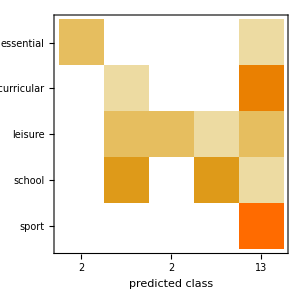

```mathematica
results1["ConfusionMatrixPlot"]
```

```mathematica
{test2,c[#]&/@test2}//Transpose//TableForm
```

covfefe | leisure
ieatass | leisure
canyoudecodethislol | leisure
paino | leisure
play the voilaon  | extracurricular
listen to the clelo | extracurricular
finish meth homework | sport
finish meth | sport
finish  | school
finnish | leisure
abcdefjkl; | essential
mynameisjeff | leisure
fuckyou | leisure
bitchass | leisure
isthisgoodtestingdata | leisure
whyareyoureadingthis | leisure
stopreadingthis | leisure
this is for the machine, Adam, stop | extracurricular
mynameisJeff once again | sport
I eata sss | school
pingpang | leisure
horsebackridoignw  | school
english S.A. | school
S.A. | leisure
I'm going to watch SPONGeBab | school
I'm going to watch a documentairee | extracurricular

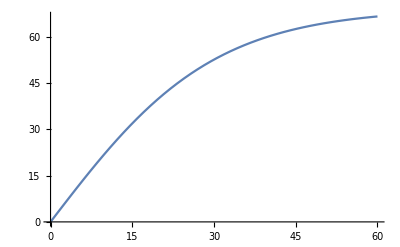

```mathematica
Plot[69*2(LogisticSigmoid[x/15]-.5),{x,0,60}]
```

```mathematica
Export["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\sigmoid.csv",Table[69*2(LogisticSigmoid[x/15]-.5),{x,0,60}]//Round]
```

C:\Users\Adam Yu\source\repos\PeacefulExpedition\sigmoid.csv